## Load Data

```mathematica
ClearAll["Global`*"]
mydata=Import[StringJoin[NotebookDirectory[],"data/ExampleFreezeOut.mx"]];
Keys[mydata]

dαs=mydata["Alpha"][[2;;]]-mydata["Alpha"][[1;;-2]];
αs=mydata["Alpha"];
urs=Sinh[ArcTanh[(Transpose@mydata["BackgroundFields"])[[1]]]]; (*dimensionless*)
uτs=Cosh[ArcTanh[(Transpose@mydata["BackgroundFields"])[[1]]]]; (*dimensionless*)
rs=mydata["Radius"];(*in IGeV*)
Drs=mydata["RadialDerivative"];(*in IGeV*)
τs=mydata["Time"];(*in IGeV*)
Dτs=mydata["TimeDerivative"];(*in IGeV*)
```

{BackgroundFields,Alpha,Time,Radius,NumberOfPoints,TimeDerivative,RadialDerivative,MidpointRule,rStart,tStart,CentralityClass}

```mathematica
headers={"alpha","tau","r","Dtau","Dr","ur","utau"};
data=Transpose@{
αs,(*dimensionless*)
τs,(*in fm/c*)
rs,(*in fm*)
Dτs,(*in fm/c*)
Drs,(*in fm*)
urs,
uτs
};
exportdata=Prepend[data,headers];
Export[StringJoin[NotebookDirectory[],"data/ExampleFreezeOut.csv"],exportdata,"CSV"];
Export[StringJoin[NotebookDirectory[],"data/ExampleFreezeOut.txt"],{
{1,2,3},{10,20,30}},
"List"];
(*FreezeOutPlot=ListPlot[Transpose[{mydata["Radius"],mydata["Time"]}],AxesLabel->{r,τ}]*)
```

The αs are not at all evenly spaced and their spacing varies quite discontinuously.

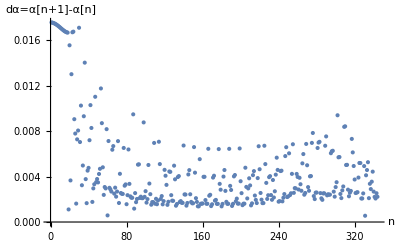

```mathematica
(*ListPlot[Transpose@{αs[[1;;-2]],dαs},AxesLabel->{"α","dα"}]*)
ListPlot[dαs,AxesLabel->{"n","dα=α[n+1]-α[n]"}]
```

### Define Interpolating Functions from the Data

NOTATION: an object named "fs" (where "f" stands for any of τ,α,ur,...) refers to an array of values of the corresponding quantity evaluated on the freezeout surface, as a function of α. So Transpose{αs,fs} are the (x,y)-value pairs corresponding to the function f[α]. Here we reconstruct the corresponding functions from interpolation, assuming they are sufficiently smooth and well resolved. The necessity of interpolated functions on the FO surface becomes clear later on.

```mathematica
ur=Interpolation[Transpose@{αs,urs}];
uτ=Interpolation[Transpose@{αs,uτs}];
r=Interpolation[Transpose@{αs,rs}];
Dr=Interpolation[Transpose@{αs,Drs}];
τ=Interpolation[Transpose@{αs,τs}];
Dτ=Interpolation[Transpose@{αs,Dτs}];
```

## Compute Field on Freezeout Surface

```mathematica
GeVtoIfm=5.0677;(*5.0677;(*1GeV=5.0677(fm^-1)\[hbar]c*)*)
IfmtoGeV=1/GeVtoIfm;
fmtoIGeV=GeVtoIfm;
IGeVtofm=1/fmtoIGeV;
mσ=0.3;(*mass of the sigma field ~ 400-800 MeV*)
ϵ=0.01*0.160054;(*energy density at freeze out in GeV/(fm^3)*)
vev=0.05;(*??? vev of sigma field ??? pion decay constant ~92MeV ???, in GeV*)
χ2=(-mσ^2+2*mσ*Sqrt[3*ϵ*(IfmtoGeV^3)/vev^2+mσ^2])/6;(*in GeV^2*)
χ=Sqrt[χ2];(*in GeV*)
(*θ0=0.5; This will be taken care of later*)

(*θ[α_?NumericQ]:=χ*NIntegrate[(Dτ[αprime]uτ[αprime]-Dr[αprime]*ur[αprime])*fmtoIGeV,{αprime,0,α}];*)
ρ=Sqrt[vev*(2*χ2+mσ^2)/(mσ^2)];(*in GeV*)
(*ϕfreezes:=ρ*Exp[I*θs];(*in GeV*)
π0s:=Sqrt[2]*Im[ϕfreezes];(*in GeV*)
σ0s:=Sqrt[2]*Re[ϕfreezes];(*in GeV*)*)
```

Evaluating θ via numerical integration seems to be very slow. This is a problem: Later a call to NIntegrate[(some function of θ[α]),{α, ... , ... }] is necessary (discussion later), but nested calls to NIntegrate a slow and "nesty" :)

```mathematica
θ[α_?NumericQ]:=χ*NIntegrate[(Dτ[αprime]uτ[αprime]-Dr[αprime]*ur[αprime])*fmtoIGeV,{αprime,0,α}]
result=Timing[ListPlot[Transpose@{#,θ[#]}&/@Range[0,Pi/2,0.05]]];
Print[result[[1]], " seconds"]
Show[result[[2]]]
```

$Aborted

Part::partd: Part specification result⟦1⟧ is longer than depth of object.

result⟦1⟧ seconds

Part::partd: Part specification result⟦2⟧ is longer than depth of object.

Show::gtype: Part is not a type of graphics.

Show[result⟦2⟧]

Performing the integration via Accumulate is faster, but since dα is not very continuous, so is the accumulated result. The resulting function is not nicely interpolated.

{Null}

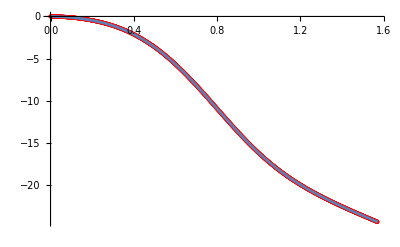

```mathematica
θaccs=χ*Accumulate[(Dτs*uτs-Drs*urs)[[1;;-2]]*fmtoIGeV*dαs];(*dimensionless*)
Quiet[
{θacc=Interpolation[Transpose@{αs[[1;;-2]],θaccs}];},
{InterpolatingFunction::dmval}
]
Show[
ListPlot[Transpose@{αs[[1;;-2]],θaccs},PlotStyle->{Directive[Red,PointSize[Medium]]}],
Plot[θacc[α],{α,0,Pi/2}]
]
```

It is useful to FIRST interpolate the input data and generate evenly spaced α values and SECOND use numerical integration via Accumulate.

```mathematica
Quiet[
{
(*Why does this not work with "=" instead of ":="*)
logspace[a_,b_,n_]:=10.0^Range[a,b,(b-a)/(n-1)];
     linspace[a_,b_,n_]:=Range[a,b,(b-a)/(n-1)];

Nαs=1500;
αs=linspace[0,Pi/2,Nαs];
dαs=(Pi/2)/Nαs;
urs=ur[αs]; (*dimensionless*)
uτs=uτ[αs]; (*dimensionless*)
rs=r[αs];(*in IGeV*)
Drs=Dr[αs];(*in IGeV*)
τs=τ[αs];(*in IGeV*)
Dτs=Dτ[αs];
},
{InterpolatingFunction::dmval}]
```

{Null}

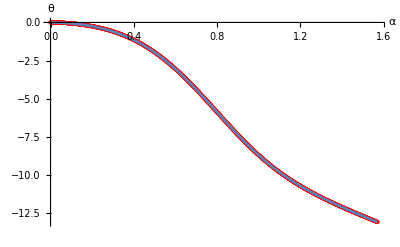

```mathematica
θaccs=χ*Accumulate[(Dτs*uτs-Drs*urs)*fmtoIGeV*dαs];(*dimensionless*)
θacc=Interpolation[Transpose@{αs,θaccs}];
Show[
ListPlot[Transpose@{αs,θaccs},PlotStyle->{Directive[Red,PointSize[Medium]]},AxesLabel->{α,θ}],
Plot[θacc[α],{α,0,Pi/2},AxesLabel->{α,θ}]
]
```

The result can now be used to define the sigma and pion fields on the freezeout surface.

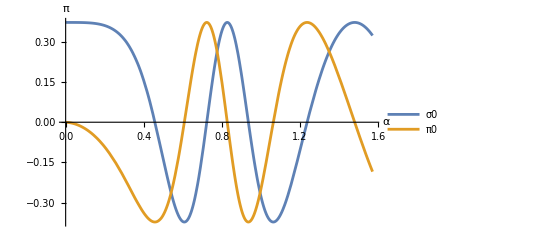

```mathematica
ϕ0[α_]=ρ*Exp[I*θacc[α]];(*in GeV*)
π0[α_]=Sqrt[2]*Im[ϕ0[α]];(*in GeV*)
σ0[α_]=Sqrt[2]*Re[ϕ0[α]];(*in GeV*)
Plot[{σ0[α],π0[α]},{α,0,Pi/2},
PlotLegends->{σ0,π0},
AxesLabel->{α,Pi}]
```

### What about these error messages due to nested calls to NIntegrate?

```mathematica
f[x_?NumericQ]:=NIntegrate[t,{t,0,x}](*1/2 x^2*)
k[x_?NumericQ]:=Re[f[x]]
h=NIntegrate[Evaluate[k[x]],{x,0,1}]
```

0.166667

```mathematica
f[x_?NumericQ]:=NIntegrate[t,{t,0,x}](*1/2 x^2*)
h=NIntegrate[Evaluate[f[x]],{x,0,1}]
```

0.166667

```mathematica
g[y_]:=NIntegrate[f[x],{x,0,y}]
g[1]
```

0.166667

## Compute the Fourier Spectrum of the Source

First, define a set of helper functions. These depend on the (transverse) momentum p_ and the coordinate α_ on the Freezeout surface. Eventually we wish to integrate over the Freezeout surface. The dependence on p_ can be substituted by explicit evaluation on a (nicely resolved) grid in momentum space. The dependence on α_ must remain symbolic, since we wish to numerically integrate over α_ using NIntegrate.

```mathematica
mπ=0.14;(*in GeV, mπ0=134.9768 MeV, mπ+-=139.57039 MeV *)
ω[p_]=Sqrt[p^2+mπ^2];(*in GeV (p in GeV) *)
J0rp[α_,p_]=BesselJ[0,r[α]*p*GeVtoIfm];(*dimensionless*)
J1rp[α_,p_]=BesselJ[1,r[α]*p*GeVtoIfm];(*dimensionless*)
Y0tw[α_,p_]=BesselY[0,τ[α]*ω[p]*GeVtoIfm];(*dimensionless*)
Y1tw[α_,p_]=BesselY[1,τ[α]*ω[p]*GeVtoIfm];(*dimensionless*)
J0tw[α_,p_]=BesselJ[0,τ[α]*ω[p]*GeVtoIfm];(*dimensionless*)
J1tw[α_,p_]=BesselJ[1,τ[α]*ω[p]*GeVtoIfm];(*dimensionless*)

H1[α_,p_]=J0rp[α,p]*(-Y0tw[α,p]+I*J0tw[α,p]);(*dimensionless*)
H2[α_,p_]=Dτ[α]*fmtoIGeV*p*J1rp[α,p]*(-Y0tw[α,p]+I*J0tw[α,p])+(*dimensionless*)
Dr[α]*fmtoIGeV*J0rp[α,p]*ω[p]*(-Y1tw[α,p]+I*J1tw[α,p]);(*dimensionless*)
```

NOTATION: an object named "fps" with f some quantity represents a function f[p_,...] with the p_-dependence evaluated explicitly on the momentum grid given by "ps".

```mathematica
ps=linspace[0,2,50];
Print[Min[ps]," to ",Max[ps], " GeV"]
```

0 to 2 GeV

```mathematica
(*σ0=σfreeze*Cos[θ0]-πfreeze*Sin[θ0]
π0=πfreeze*Cos[θ0]+σfreeze*Sin[θ0]*)
H1ps[α_]=H1[α,ps];
H2ps[α_]=H2[α,ps];
```

The most ressource heavy computation happens here, due to the use of NIntegrate. The routine (probably) uses more and more subdivisions for the large-p_ components in H(1/2)ps.

WHY USE NINTEGRATE AND INTERPOLATED FUNCTIONS? Discrete Fourier Transform, say  on  an  Interval [0, L], discretized  with  N  points, shows  and  alias  effect  and  is  valid  only  up  to  the  Nyquist  frequency  (~ momentum)  (2?)  Nπ/L  and  the  spectrum  will  then  continue  periodically  (just  as  the  real  space  function  will, if  calculated  from  discretized  momentum  grid . There  will  thus  be  no  convergence  to  0  for  large  momenta . It  is  not  immediately  clear  to  me  how  this  effect  is  altered  when  using  Bessel  functions  and  the  integral  measure  in  polar  coordinates, but  qualitatively  this  should  prevent  convergence  to  0  of  the  spectrum  for  large  p, which  would  be  necessary  for  a  physical  spectrum . 
    
    One  could  simply  apply  a  finer  discretization  in  real  space  (= finer  mesh  of  αs), but  I  expect  the  effect  to  be  worse  for  larger  momenta . The  routine  NIntegrate  automatically  chooses  and  refines  the  grid  of  αs  in  real  space, until  the  integral  has  converged  sufficiently  well . For  low  p_  it  is  expected  that  the  grid  specified  by  the  raw  data  is  enough . For  large  p_  a  finer  grid  should  be  chosen . We  should  thus  provide  (interpolated)  functions  of  α_  such  that  this  refinement  through  the  integration  routine is dynamically possible .

```mathematica
(*The C's all have dimension IGeV*)
{time1,C1σps}=Timing[2*Pi^2*NIntegrate[τ[α]*r[α]*fmtoIGeV^2*(-1)*π0[α]*χ*(-Dr[α]*uτ[α]+Dτ[α]*ur[α])*H1ps[α],{α,0,Pi/2}]];
Print[time1, " seconds"]
{time2,C1πps}=Timing[2*Pi^2*NIntegrate[τ[α]*r[α]*fmtoIGeV^2*σ0[α]*χ*(-Dr[α]*uτ[α]+Dτ[α]*ur[α])*H1ps[α],{α,0,Pi/2}]];
Print[time2, " seconds"]
{time3,C2σps}=Timing[2*Pi^2*NIntegrate[τ[α]*r[α]*fmtoIGeV^2*σ0[α]*H2ps[α],{α,0,Pi/2}]];
Print[time3, " seconds"]
{time4,C2πps}=Timing[2*Pi^2*NIntegrate[τ[α]*r[α]*fmtoIGeV^2*π0[α]*H2ps[α],{α,0,Pi/2}]];
Print[time4, " seconds"]
(*
C1σ=2*Pi^2*Total[dalpha*taus*rs*fmtoIGeV^2*((-1)*π0*χ*(-drs*utau+dtaus*ur)*H1ps)];(*I guess u_tau=-u^tau*)
C1π=2*Pi^2*Total[dalpha*taus*rs*fmtoIGeV^2*(σ0*χ*(-drs*utau+dtaus*ur)*H1ps)];
C2σ=2*Pi^2*Total[dalpha*taus*rs*fmtoIGeV^2*σ0*H2ps];
C2π=2*Pi^2*Total[dalpha*taus*rs*fmtoIGeV^2*π0*H2ps];
*)

Jps[θ0_]=(C1σps+C2σps)*Sin[θ0]+(C1πps+C2πps)*Cos[θ0];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {1.09831}. NIntegrate obtained 91.6736+54.6516 ⅈ and 0.00224251 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {1.09831}. NIntegrate obtained 59.2937+77.8191 ⅈ and 0.000774676 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {1.09831}. NIntegrate obtained -28.3103+70.3083 ⅈ and 0.000797146 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

20.6477 seconds

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {1.11671}. NIntegrate obtained 12.9414+21.0819 ⅈ and 0.00293993 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {1.11671}. NIntegrate obtained 7.85538+30.8246 ⅈ and 0.00103261 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {1.11671}. NIntegrate obtained -39.0399+39.7518 ⅈ and 0.00101265 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

17.9868 seconds

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained -16.0861-7.84662 ⅈ and 0.0221431 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained -67.8543+28.7908 ⅈ and 0.0137173 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained -185.511-92.5917 ⅈ and 0.0108076 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

25.8698 seconds

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.681063}. NIntegrate obtained 252.236-192.52 ⅈ and 0.0105093 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.681063}. NIntegrate obtained 245.062-122.305 ⅈ and 0.00502202 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.681063}. NIntegrate obtained 156.283+34.3524 ⅈ and 0.00476859 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

37.8608 seconds

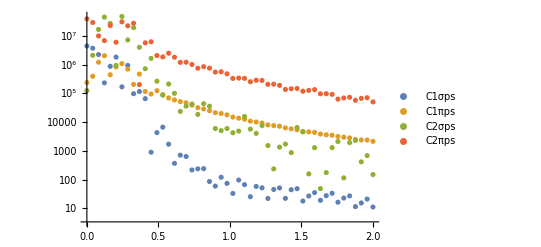

```mathematica
ListLogPlot[
{Transpose@{ps,Abs[C1σps]^2},
Transpose@{ps,Abs[C1πps]^2},
Transpose@{ps,Abs[C2σps]^2},
Transpose@{ps,Abs[C2πps]^2}},
PlotLegends->{"C1σps","C1πps","C2σps","C2πps"}
]
```

```mathematica
Quiet[
{Manipulate[
ListLogPlot[Transpose@{ps,Abs[Jps[θ0]]^2},AxesLabel->{"p [GeV]","|π(p)|^2"}]
,{θ0,0,2*Pi}]
},{Transpose::nmtx}]
```

{}

Transpose::nmtx: The first two levels of {{0,1/99,2/99,1/33,4/99,5/99,2/33,7/99,8/99,1/11,«90»},Abs[Jps[0]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.,0.010101,0.020202,0.030303,0.040404,0.0505051,0.0606061,0.0707071,0.0808081,0.0909091,«90»},Abs[Jps[0.]]^2} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLogPlot::lpn: Transpose[{{0,0.0101010101010101,0.0202020202020202,0.0303030303030303,0.0404040404040404,0.05050505050505051,0.06060606060606061,0.07070707070707071,0.08080808080808081,0.09090909090909091,«90»},Abs[Jps[0]]^2}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {{0,1/99,2/99,1/33,4/99,5/99,2/33,7/99,8/99,1/11,«90»},Abs[Jps[0]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.,0.010101,0.020202,0.030303,0.040404,0.0505051,0.0606061,0.0707071,0.0808081,0.0909091,«90»},Abs[Jps[0.]]^2} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLogPlot::lpn: Transpose[{{0,0.0101010101010101,0.0202020202020202,0.0303030303030303,0.0404040404040404,0.05050505050505051,0.06060606060606061,0.07070707070707071,0.08080808080808081,0.09090909090909091,«90»},Abs[Jps[0]]^2}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {{0,1/99,2/99,1/33,4/99,5/99,2/33,7/99,8/99,1/11,«90»},Abs[Jps[0]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.,0.010101,0.020202,0.030303,0.040404,0.0505051,0.0606061,0.0707071,0.0808081,0.0909091,«90»},Abs[Jps[0.]]^2} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLogPlot::lpn: Transpose[{{0,0.0101010101010101,0.0202020202020202,0.0303030303030303,0.0404040404040404,0.05050505050505051,0.06060606060606061,0.07070707070707071,0.08080808080808081,0.09090909090909091,«90»},Abs[Jps[0]]^2}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {{0,1/99,2/99,1/33,4/99,5/99,2/33,7/99,8/99,1/11,«90»},Abs[Jps[0]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.,0.010101,0.020202,0.030303,0.040404,0.0505051,0.0606061,0.0707071,0.0808081,0.0909091,«90»},Abs[Jps[0.]]^2} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLogPlot::lpn: Transpose[{{0,0.0101010101010101,0.0202020202020202,0.0303030303030303,0.0404040404040404,0.05050505050505051,0.06060606060606061,0.07070707070707071,0.08080808080808081,0.09090909090909091,«90»},Abs[Jps[0]]^2}] is not a list of numbers or pairs of numbers.

## All of the Above In a Single Function

```mathematica
(*
π0=...;
Dπ0=σ0[α]*χ*(-Dr[α]*uτ[α]+Dτ[α]*ur[α]);
*)
ComputeSourceSpectr[ps_,f_,Df_]:=Module[{H1ps,H2ps,spectrps},
(*
f is supposed to be the π-field, Df it's perpendiculat derivative, 
Df = r'*D[f,τ]+τ'*D[f,r]

The name π is protected!!!
*)
H1ps[α_]=H1[α,ps];
H2ps[α_]=H2[α,ps];

spectrps=2*Pi^2*NIntegrate[
τ[α]*r[α]*fmtoIGeV^2*(Df[α]*H1ps[α]+f[α]*H2ps[α]),{α,0,Pi/2},
Method->{Automatic,"SymbolicProcessing"->0}
];
spectrps
]
```

```mathematica
ps=linspace[0,1,100];
Jπspec=ComputeSourceSpectr[ps,π0[#]&,σ0[#]*χ*(-Dr[#]*uτ[#]+Dτ[#]*ur[#])&];
Jσspec=ComputeSourceSpectr[ps,σ0[#]&,-1*π0[#]*χ*(-Dr[#]*uτ[#]+Dτ[#]*ur[#])&];
Jπspecfinal[θ0_]=Jσspec*Sin[θ0]+Jπspec*Cos[θ0];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained 145.454-438.218 ⅈ and 0.0123975 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained 157.688-428.96 ⅈ and 0.0119643 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained 190.598-399.657 ⅈ and 0.0108487 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {1.09831}. NIntegrate obtained -234.295+100.648 ⅈ and 0.00713875 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {1.09831}. NIntegrate obtained -235.797+92.3522 ⅈ and 0.00676721 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {1.09831}. NIntegrate obtained -238.963+69.1501 ⅈ and 0.00591238 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

This does exactly the same as before:

```mathematica
Manipulate[
ListLogPlot[
Transpose@{ps,Abs[Jπspecfinal[θ0]]^2},
AxesLabel->{"p [GeV]","|π(p)|^2"}],
{θ0,0,2*Pi}]
```

```mathematica
Quiet[
{Manipulate[
ListLogPlot[
{Transpose@{ps,Abs[Jπspecfinal[θ0]]^2},Transpose@{ps,Abs[Jps[θ0]]^2}},
PlotMarkers->{{Graphics[{Red,Circle[]}],0.04},{Graphics[{Blue,Rectangle[]}],0.02}}
,AxesLabel->{"p [GeV]","|π(p)|^2"}]
,{θ0,0,2*Pi}]
},{Transpose::nmtx}]
```

{}

Transpose::nmtx: The first two levels of {{0,1/99,2/99,1/33,4/99,5/99,2/33,7/99,8/99,1/11,«90»},Abs[Jps[0]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,0.0101010101010101,0.0202020202020202,0.0303030303030303,0.0404040404040404,0.05050505050505051,0.06060606060606061,0.07070707070707071,0.08080808080808081,0.09090909090909091,«90»},Abs[Jps[0]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.,0.010101,0.020202,0.030303,0.040404,0.0505051,0.0606061,0.0707071,0.0808081,0.0909091,«90»},Abs[Jps[0.]]^2} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLogPlot::lpn: {{{0,20.6201},{0.0101010101010101,20.5398},{0.0202020202020202,20.2936},{0.0303030303030303,19.8639},{0.0404040404040404,19.212},{«1»},{«44»,«19»},{0.07070707070707071,16.2233},{0.08080808080808081,16.9131},{0.09090909090909091,17.2781},«90»},«1»} is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {{0,1/99,2/99,1/33,4/99,5/99,2/33,7/99,8/99,1/11,«90»},Abs[Jps[0]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.,0.010101,0.020202,0.030303,0.040404,0.0505051,0.0606061,0.0707071,0.0808081,0.0909091,«90»},Abs[Jps[0.]]^2} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLogPlot::lpn: {{{0,21.0444},{0.0101010101010101,21.0397},{0.0202020202020202,21.0181},{0.0303030303030303,20.9573},{0.0404040404040404,20.8192},{«1»},{«44»,«18»},{0.07070707070707071,19.1191},{0.08080808080808081,17.122},{0.09090909090909091,17.7081},«90»},«1»} is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {{0,1/99,2/99,1/33,4/99,5/99,2/33,7/99,8/99,1/11,«90»},Abs[Jps[0]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.,0.010101,0.020202,0.030303,0.040404,0.0505051,0.0606061,0.0707071,0.0808081,0.0909091,«90»},Abs[Jps[0.]]^2} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLogPlot::lpn: «1» is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {{0,1/99,2/99,1/33,4/99,5/99,2/33,7/99,8/99,1/11,«90»},Abs[Jps[0]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.,0.010101,0.020202,0.030303,0.040404,0.0505051,0.0606061,0.0707071,0.0808081,0.0909091,«90»},Abs[Jps[0.]]^2} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLogPlot::lpn: «1» is not a list of numbers or pairs of numbers.

## Come up with different initial conditions?

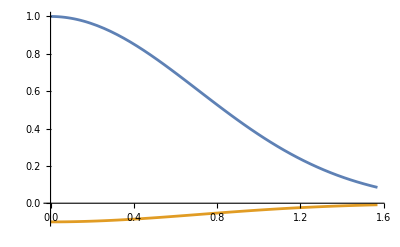

```mathematica
πinitial[α_]:=Exp[-α^2];
Dπinitial[α_]:=-0.1*πinitial[α];
ps=linspace[0,2,50];
Plot[{πinitial[α],Dπinitial[α]},{α,0,Pi/2}]
```

```mathematica
Jπspec=ComputeSourceSpectr[ps,πinitial[#]&,Dπinitial[#]&];
```

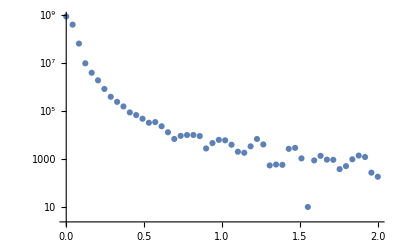

```mathematica
ListLogPlot[Transpose@{ps,Abs[Jπspec]^2}]
```

```mathematica
Abs@Jπspec^2
```

{1.19476×10^9,4.97032×10^6,18598.3,39892.7,21801.,2350.7,20478.9,97.0901,28.3285,3795.23,2999.95,823.326,1122.57,4539.83,1301.98,3247.32,1434.33,2514.41,1556.64,2691.96,182.523,11.9267,507.303,790.218,51.0108,1200.97,2398.25,227.218,1861.2,219.471,155.816,768.617,257.697,998.7,392.785,125.687,642.148,125.071,119.542,129.07,67.1037,507.75,99.4942,381.432,1143.22,136.777,860.426,323.45,86.229,470.331}

## Compare to Alice Data

```mathematica
Alicedatatxt=Import[StringJoin[NotebookDirectory[],"data/HEPData-ins1222333-v1-Table_1.csv"],"Text"];
(*Alicedata=ImportString[StringReplace[StringReplace[Alicedatatxt,RegularExpression["\n+"]->"\n"],StartOfLine~~"#"~~Shortest[___]~~EndOfLine~~"\n"->""],"CSV"];*)
Alicedata=ImportString[StringReplace[Alicedatatxt,StartOfLine~~"#"~~Shortest[___]~~EndOfLine~~"\n"->""],"CSV","IgnoreEmptyLines"->True];
MatrixForm[Alicedata];
titles=Alicedata[[1]];
enumeratedtitles=Transpose[{Range[Length[titles]],titles}]
πplus=Alicedata[[2;;42]];
πminus=Alicedata[[44;;]];
aliceps=(Transpose@πplus)[[1]];
aliceyieldplus=(Transpose@πplus)[[4]];
aliceyieldminus=(Transpose@πminus)[[4]];
```

{{1,PT [GEV]},{2,PT [GEV] LOW},{3,PT [GEV] HIGH},{4,(1/Nev)*(1/(2*PI*PT))*D2(N)/DPT/DYRAP [GEV**-2]},{5,stat +},{6,stat -},{7,sys +},{8,sys -},{9,sys,normalization uncertainty +},{10,sys,normalization uncertainty -}}

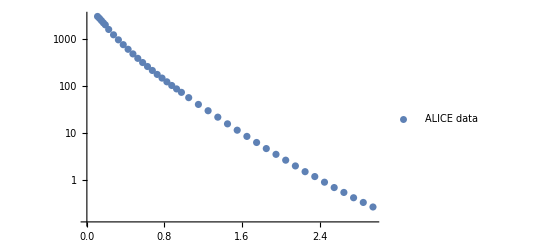

```mathematica
ListALICE=Transpose@{aliceps,aliceyieldplus+aliceyieldminus};
ListLogPlot[
ListALICE,
PlotLegends->{"ALICE data"}
]
```

```mathematica
Quiet[
{Manipulate[
ListLogPlot[
{ListALICE,Transpose@{ps,1/(2*Pi)^3*Abs[Jπspecfinal[θ0]]^2}},
PlotLegends->{"ALICE","myspectr"}
],{θ0,0,2*Pi}]
},{Transpose::nmtx}]
```

{}

ListLogPlot::lpn: {{},{{0,11.519},{0.0101010101010101,11.5052},{0.0202020202020202,11.4697},{0.0303030303030303,11.424},{0.0404040404040404,11.3699},«1»,{«44»,«19»},{0.07070707070707071,10.9988},{0.08080808080808081,10.8165},{0.09090909090909091,10.6938},«90»}} is not a list of numbers or pairs of numbers.